## The behavior of an imperfect predictor.

We have seen that this model performs well when it has the right parameters. But humans may have imperfect estimations of H. How does this affect the model?
You can play with the values of σ, hTrue, and hSubj to find out.

```mathematica
Remove["Global`*"]
```

### First, set the parameters.

```mathematica
μ=342;
σ=200;
hTrue=.01;
hSubj=.01;
m=200;
w=1366;
h=768;
```

### Then, generate some random data to simulate the behavior of the eggs in each trial.

```mathematica
r=RandomVariate[UniformDistribution[{0,1}],m];
```

```mathematica
switch=Table[If[r[[i]]>hTrue,0,1],{i,1,m}];
dist={};
val=1;
For[i=1,i≤m,i++,
If[switch[[i]]==1,
val=If[val==1,2,1]
];
dist=Append[dist,val]
]
x=Table[If[dist[[i]]==1,RandomVariate[NormalDistribution[μ,σ],1],RandomVariate[NormalDistribution[-μ,σ],1]],{i,1,m}];
x=Transpose[x]//Flatten;
y=Table[If[dist[[i]]==1,RandomVariate[NormalDistribution[0,σ],1],RandomVariate[NormalDistribution[0,σ],1]],{i,1,m}];
y=Transpose[y]//Flatten;
```

### The following plot shows the x-coordinate of the egg in each trial

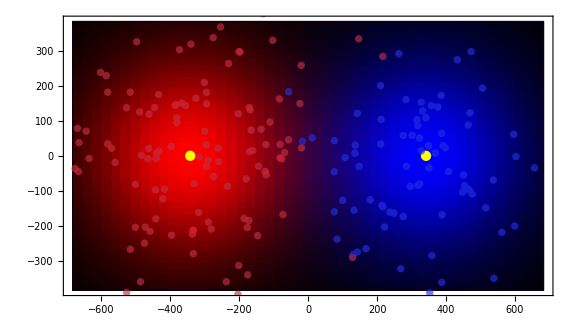

```mathematica
col=Table[If[dist[[i]]==1,Blue,Red],{i,1,m}];
pL[x_,y_]:=PDF[NormalDistribution[-μ,σ],x]* PDF[NormalDistribution[0,σ],y];
pR[x_,y_]:=PDF[NormalDistribution[μ,σ],x]* PDF[NormalDistribution[0,σ],y];
rFun[x_,y_]:=Round[pL[x,y]/pL[-μ,0],.001];
bFun[x_,y_]:=Round[pR[x,y]/pR[μ,0],.001];
cFun=Function[{x,y},RGBColor[rFun[x,y],0,bFun[x,y]]];
Show[
ParametricPlot[{x,y},{x,-w/2,w/2},{y,-h/2,h/2},ColorFunctionScaling->False,ColorFunction->cFun, Axes->False,PlotPoints->50, ImageSize->Large],
ListPlot[{{-μ,0},{μ,0}}, PlotStyle->Yellow],
ListPlot[Table[Style[{x[[i]],y[[i]]}, col[[i]]],{i,1,m}], PlotStyle->Opacity[.4]]
]
```

Following is a plot of the x-position of each egg over time. The color of each point marks which chicken is correct on that round.

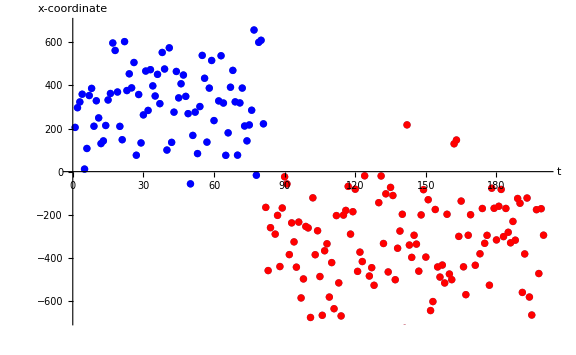

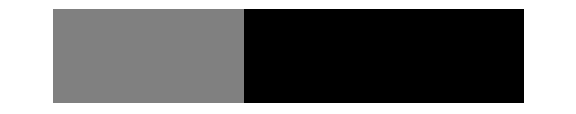

```mathematica
ListPlot[Table[Style[x[[i]], col[[i]]],{i,1,m}], PlotRange->{-683,683},Joined->False,AxesLabel->{"t","x-coordinate"}, ImageSize->Large]
ArrayPlot[{dist}, ImageSize->Large]
```

### Now, based on the data above, the model will make a prediction of which chicken the egg came from.

The model represents expected participant response based on their subjective H. The following simulates participant response using the model.

```mathematica
l[1]=0;
For[n=2,n≤m,n++,
ψ[n]=l[n-1]+Log[(1-hSubj)/hSubj+Exp[-l[n-1]]]-Log[(1-hSubj)/hSubj+Exp[l[n-1]]]//N;
llr[n]=-2*(LogLikelihood[NormalDistribution[μ,σ],{x[[n]]}]-LogLikelihood[NormalDistribution[-μ,σ],{x[[n]]}])//N;
l[n]=ψ[n]+llr[n];
]
```

### The plot below demonstrates how the belief of the model changes over time in response to changes in the environment.

Below is a plot of Ln. This represents belief and the strength of the belief of which chicken is the correct chicken. The green dots represent correct answers and the red dots represent incorrect answers.

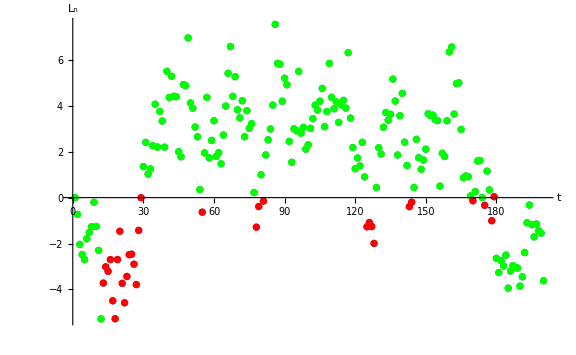

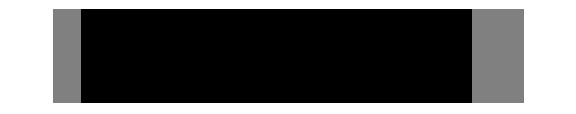

```mathematica
pred=Table[If[l[i]>0,2,1],{i,1,m}];
col=Table[If[dist[[i]]==pred[[i]],Green,Red],{i,1,m}];
ListPlot[Table[Style[l[i],col[[i]]],{i,1,m}],Joined->False,AxesLabel->{"t","L_n"}, ImageSize->Large]
ArrayPlot[{dist}, ImageSize->Large]
```

```mathematica
pred=Table[If[l[i]>0,2,1],{i,1,m}];
```

### Percent correct:

```mathematica
Sum[If[dist[[i]]==pred[[i]],1,0],{i,1,m}]/m//N
```

0.845

### Histograms

We want to get a better idea of how H influences participant response. So, we plot the magnitude of ψ across trials as well as the magnitude of LLR across trials.

Below is a histogram of ψ across trials.

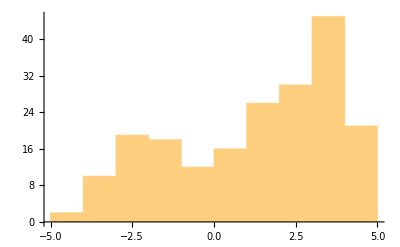

```mathematica
ψlist=Table[ψ[i],{i,2,m}];
Histogram[ψlist]
```

Below is a histogram of LLR across trials.

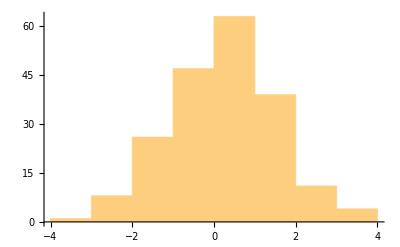

```mathematica
llrlist=Table[llr[i],{i,2,m}];
Histogram[llrlist]
```

Below is the above two plot overlaid.

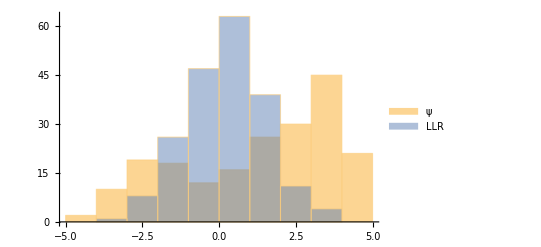

```mathematica
Histogram[{ψlist,llrlist},ChartLegends->{"ψ","LLR"}]
```

It appears that LLR tends to be higher in magnitude than ψ on average. To test this assumption, we look at the distribution of |ψ| - |LLR|. If ψ tends to have greater influence (magnitude) than LLR, then the Histogram will have many more positive values than negative.

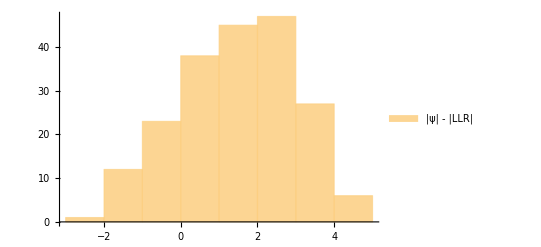

```mathematica
Histogram[{Abs[ψlist]-Abs[llrlist]},ChartLegends->{"|ψ| - |LLR|"}]
```

Note that with a small σ, it doesn’t matter how poor the prediction of H; the eggs appear so close to the chickens that H ends up having little influence on the decision. This is because LLR_n will always be larger in magnitude than ψ. Notice how the majority of the time, ψ does not influence the sign of Ln.

Below is shown the number of times adding ψ to the estimation did not affect the prediction.

```mathematica
Total[Table[If[TrueQ[Sign[ψ[n]+llr[n]]==Sign[llr[n]]],1,0],{n,2,m}]]/200//N
```

0.645